```mathematica
data={166,188.2,158,129,212.9,165.9,105,160,137.9,212.96,212.96,212.96,2181.7,632.9,1522.9,825.9,700.7,668.9,1240,743,601.1,686.1,726.7,729.2,719.1,1275,1275,1275,1275,130,264,887.2,683.2,299,290,550,646};
Length[data]
```

37

```mathematica
Needs["MaTeX`"]
```

```mathematica
speciesNames={"Rhytidoponera aurata","Pogonomyrmex rugosus","Pogonomyrmex rugosus","Pogonomyrmex maricopa","Paraponera clavata","Pachycondyla berthoudi","Myrmecocystu mexicanus","Myrmecocystu mendax","Messor pergandei","Leptogenys schwabi","Leptogenys nitida","Leptogenys attenuata","Formica rufa","Formica polyctena","Formica fusca","Cataglyphis fortis","Cataglyphis bombycina","Cataglyphis bicolor","Cataglyphis albicans","Camponotus sp","Camponotus rufipes","Camponotus herculeanus","Camponotus herculeanus","Atta vollenweideri","Acromyrmex octospinosus"};

input={1,1,1,1,1,1,1,1,1,1,1,1,6,1,6,1,1,1,1,1,1,2,1,2,1};
Table[ConstantArray[Position[input,j][[1,1]],j],{j,input}]
speciesIndices=Flatten[MapIndexed[ConstantArray[First@#2,#1]&,input]]

(*speciesIndices={1,2,3,4,5,6,7,8,8,9,10,11,11,11,11,11,11,12,12,12,12,12,12,13,13,13,14,14,15,16,17,18,19,20,21,22,23};*)
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{13,13,13,13,13,13},{1},{13,13,13,13,13,13},{1},{1},{1},{1},{1},{1},{22,22},{1},{22,22},{1}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,13,13,13,13,13,14,15,15,15,15,15,15,16,17,18,19,20,21,22,22,23,24,24,25}

```mathematica
ConstantArray[2,3]
```

{2,2,2}

```mathematica
speNa=speciesNames[[#]]&/@speciesIndices
ourspecies=Flatten[Position[speNa,#]&/@{"Cataglyphis albicans","Cataglyphis bicolor","Cataglyphis fortis","Cataglyphis bombycina","Formica polyctena"}];
rules=Thread[ourspecies->ConstantArray[{PointSize[0.025],ColorData["FallColors",0.6]},5]];
pstyle=ReplacePart[Table[{PointSize[0.025],ColorData["FallColors",0.1]},Length[speciesIndices]],rules]
```

{Rhytidoponera aurata,Pogonomyrmex rugosus,Pogonomyrmex rugosus,Pogonomyrmex maricopa,Paraponera clavata,Pachycondyla berthoudi,Myrmecocystu mexicanus,Myrmecocystu mendax,Messor pergandei,Leptogenys schwabi,Leptogenys nitida,Leptogenys attenuata,Formica rufa,Formica rufa,Formica rufa,Formica rufa,Formica rufa,Formica rufa,Formica polyctena,Formica fusca,Formica fusca,Formica fusca,Formica fusca,Formica fusca,Formica fusca,Cataglyphis fortis,Cataglyphis bombycina,Cataglyphis bicolor,Cataglyphis albicans,Camponotus sp,Camponotus rufipes,Camponotus herculeanus,Camponotus herculeanus,Camponotus herculeanus,Atta vollenweideri,Atta vollenweideri,Acromyrmex octospinosus}

{{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.6917614, 0.40925940000000005, 0.22008260000000002]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.6917614, 0.40925940000000005, 0.22008260000000002]},{PointSize[0.025],RGBColor[0.6917614, 0.40925940000000005, 0.22008260000000002]},{PointSize[0.025],RGBColor[0.6917614, 0.40925940000000005, 0.22008260000000002]},{PointSize[0.025],RGBColor[0.6917614, 0.40925940000000005, 0.22008260000000002]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]},{PointSize[0.025],RGBColor[0.3169238, 0.3958158, 0.33004079999999997]}}

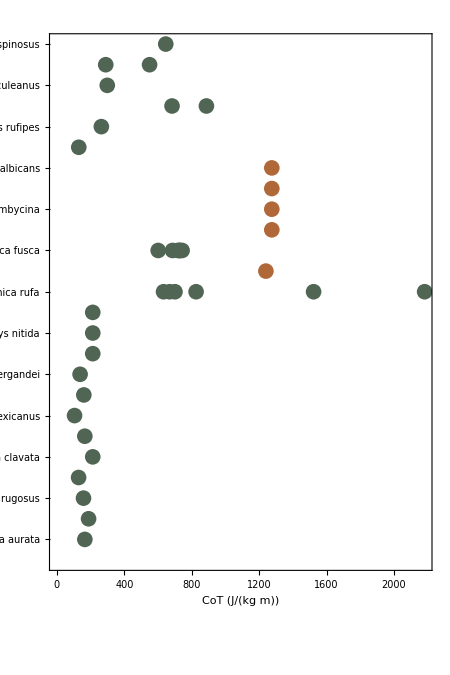

```mathematica
xtiks=DeleteDuplicates[Transpose[{speciesIndices,Map[Style[Rotate[#,0Degree],Italic,FontFamily->"Latin Modern Roman 10"]&,speNa]}]];
plot=ListPlot[MapThread[Style[#1,#2]&,(*Apply style to each point*){Transpose[{data,speciesIndices}],pstyle}],Frame->True,FrameTicks->{{xtiks,Automatic},Automatic},LabelStyle->{FontFamily->"Latin Modern Roman 10",Black,15},ImageSize->{450,450},AspectRatio->1.5,FrameLabel->{{None,None},{"CoT (J/(kg m))",None}}]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\speciesCom.pdf",plot]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\speciesCom.pdf

```mathematica
70.587
44.644, 32.437
```